```mathematica
(* Recursive Method *)
```

```mathematica
Clear[n]

fibrec[n_]:=fibrec[n-1]+fibrec[n-2];
fibrec[1]= 0;
fibrec[2]=1;

fibrec[5]
```

3

```mathematica
(* Recursive Timing *)
```

```mathematica
timerec[n_]:= Timing[fibrec[n]]
timerec[10]
```

{0.000181,34}

```mathematica
(* Recursive Space *)
```

```mathematica
Clear[n];
spacerec[n_] := ByteCount[fibrec[n]];
spacerec[25]

(* Time Constrain? *)
```

16

```mathematica
(* Recursive Time Plot *)
```

```mathematica
Clear[n, x];
timeplotrec[n_] := ListLinePlot[{Table[{f, First[timerec[f]]}, {f, 1, n}]}];

recTime[n_] := Plot[(((1+Sqrt[5])/2)^x)/10000, {x, 0, n},PlotRange->{{0, 50},{0,100000}},PlotLabel->  "Recursive Time Complexity",AxesLabel -> {"n", time}];
itTime[n_]:= Plot[x, {x, 0, n}, PlotRange->{{0, 50},{0,100}}, PlotLabel->  "Iterative Time Complexity", AxesLabel -> {"n", time}];

Manipulate[
Grid[{{recTime[n], itTime[n]}}], Initialization :>{recTime[n_] := Plot[(((1+Sqrt[5])/2)^x)/10000, {x, 0, n},PlotRange->{{0, 50},{0,100000}},PlotLabel->  "Recursive Time Complexity",AxesLabel -> {"n", time}];itTime[n_]:= Plot[x, {x, 0, n}, PlotRange->{{0, 50},{0,100}}, PlotLabel->  "Iterative Time Complexity", AxesLabel -> {"n", time}];
} {n, 0.1, 50}
	]
```

Plot::plln: Limiting value n in {x, 0, n} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

```mathematica
Clear[n];
spaceplotrec[n_] := ListLinePlot[{Table[{f, spacerec[f]}, {f, 1, n}]}];
Manipulate[spaceplotrec[n], {n, 0, 10}]
```

```mathematica
(* Recursive Tree Plot *)
```

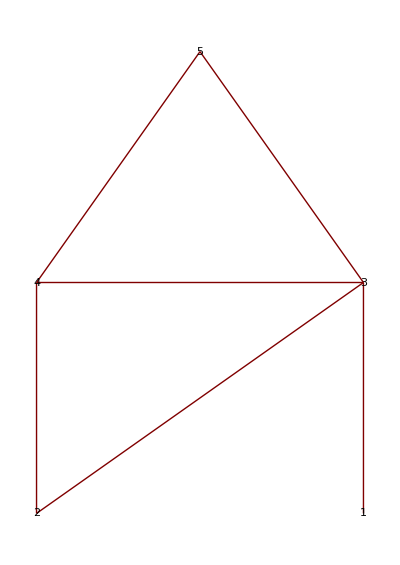

```mathematica
g={5->4,5->3,4->3,4->2,3->2,3->1};
TreePlot[g, VertexLabeling->True]
```

```mathematica
(* Iterative Method *)
```

```mathematica
Clear[fibit, i,n,a, b, c]
a = 0;
b = 1;
fibit[n_] := For[i=2,i≤n-1,i++,c=a+b; a = b;b = c]b;
First[fibit[4]]
```

2

```mathematica
(* Iterative Timing *)
```

```mathematica
timeit[n_] :=Timing[First[fibit[n]]]
timeit[4]
```

{0.00003,5}

```mathematica
(* Iterative Space *)
```

```mathematica
Clear[n]
spaceit[n_] := ByteCount[First[fibit[n]]];
spaceit[15]
```

16

```mathematica
(* Iterative Time Plot *)
```

```mathematica
Clear[n];
timeplotit[n_] := ListLinePlot[{Table[{f, First[timeit[f]]}, {f, 1, n}]}];
Manipulate[timeplotit[n], {n, 0,  60}]
```

```mathematica
(* Iterative Space Plot *)
```

```mathematica
Clear[n];
spaceplotit[n_] := ListLinePlot[{Table[{f, spaceit[f]}, {f, 1, n}]}];
Manipulate[spaceplotit[n], {n, 0, 10}]
```

```mathematica
(* Iterative Tree Plot *)
```

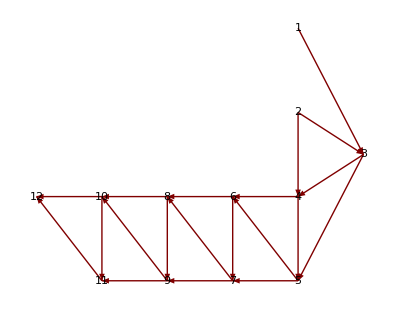

```mathematica
treeit[n_]:=Module[ {itTreeArray = {}, n0 = n} ,
					For[i=3,i≤n0,i++,AppendTo[itTreeArray, i-2 -> i];  AppendTo[itTreeArray,i-1 -> i]];
					TreePlot[itTreeArray,Right,  VertexLabeling->True, DirectedEdges->True]
				]
treeit[12]
```